```mathematica
NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"file-ops.nb"]]];
```

```mathematica
(*** PREDICTIONS ***)
Clear[predRfMonFPRTheor];

predRfMonFPRTheor[detFNR_, dInProp_, pDetNCH0_:0(* for this context *)] := 1 -(1 - detFNR + pDetNCH0)^(dInProp+1);
```

```mathematica
(*** ANALYSIS ***)
```

```mathematica
Clear[getRfFPRPointEstsWithMonH0ct, getRfFNRPointEstResidualsWithH0ct, getRfFprMSQPairsWithBins];

(* provides a list of triples: (monH0InfoCt, our RF mon FPR est, data RF mon FPR est) *) 
getRfFPRPointEstsWithMonH0ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predRfMonFPRTheor[predFNRfromData[#, detFilenames], winSize], predFPRfromData[#, monFilenames, winSize,(*mon num*)11]}&/@ sampleAcrossAllSubsets[seshNums, sampleCtPerSubset]), "h0count",monFilenames, winSize, 11];

(* KINDA USELESS: provides a list of triples: (monH1InfoCt, our mon FNR est, data mon FNR est) *) 
(*getFNRPointEstsWithDetH1ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predMonFNRTheor[predFPRfromData[#, detFilenames], winSize], predFNRfromData[#, monFilenames, winSize]}&/@ sampleAcrossAllSubsets[seshNums, sampleCtPerSubset]), "h1count",detFilenames, winSize];*)


(* provides a list of absolute residuals for above: (h1InfoCt, abs residual for our mon FNR est, abs residual for data mon FNR est) *) 
getRfFNRPointEstResidualsWithH0ct[seshNums_, sampleCtPerSubset_, winSize_] := With[{gtValue=predRfMonFPRTheor[0.1, winSize]},({#[[1]], Abs[#[[2]]-gtValue],Abs[#[[3]]-gtValue]  } & /@ getRfFPRPointEstsWithMonH0ct[seshNums, sampleCtPerSubset, winSize])];



(* privides a list of (bin start, bin elem count, mean squared error for our appr, mean squared error for data appr) ; bin end determined by bin size *) 
getRfFprMSQPairsWithBins[seshNums_, sampleCtPerSubset_, winSize_, binSize_]:= With[{h1CtTwoEstList= (*a list of triples (h0ct, our fpr est, data fpr est *) getRfFNRPointEstResidualsWithH0ct[seshNums, sampleCtPerSubset, winSize] },
(* convert h1cts into bin starts *) Flatten[#]&/@Transpose[{(Range[0,  Max@h1CtTwoEstList[[All,1]], binSize]),({Length@#, Mean@(#[[All,2]]^2), Mean@(#[[All,3]]^2)} &/@ binListsBy[h1CtTwoEstList, {First, 0, Max@h1CtTwoEstList[[All,1]]+binSize-1, binSize}])}]];
```

```mathematica
(*** PLOTS PRE CORRECTION ***) 

(* exact estimates plots *) 
(* win = 5 idk what's happening here *) 

With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 5]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, 5], Max@data[[All,1]]]]]
```

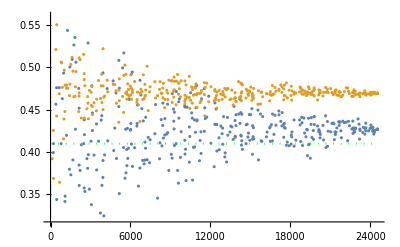

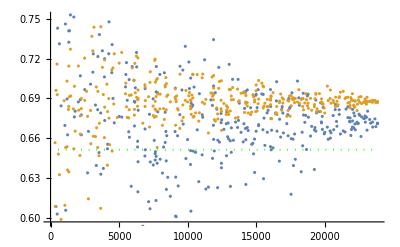

```mathematica
(* win = 10, ugh  *) 
With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, 10], Max@data[[All,1]]]]]
```

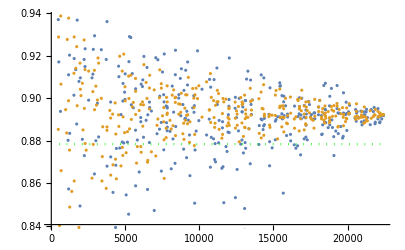

```mathematica
(* win of 20, very confused  *)
With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 20]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, 20], Max@data[[All,1]]]]]
```

```mathematica
(* MSE BINNED POST CORRECTION *)
```

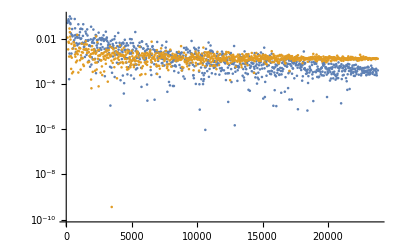

```mathematica
(* this one makes no sense at all; need bigger bins, too *) 
Clear[data];(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *)10, (* bin width *)25];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])
```